```mathematica
Guy F. Mongelli                                                                                  2/15/2013;
Prof. R.M. Sankaran                                                                      ECHE 462;
```

```mathematica
Problem Set #3;
```

```mathematica
Problem#1;
```

```mathematica
Since the parallel reactions are irreversible, the reactions selectivity will be completely dependent upon kinetic effects.  In other words, the reactions are competing and how much is formed of each product depends on the relative rates of consumption of the shared reactant.The reactions are written:
```

```mathematica
A(->)^Subscript[k, 1] B+C
```

```mathematica
A(->)^Subscript[k, 2] D+E
```

```mathematica
If 2-propanol is labelled species A, acetone is species B, hydrogen gas is species C,propene is species D, and water species E- then, the rate of change in the disappearance of species A can be written:
```

```mathematica
Subscript[dc, A]/dt=-Subscript[k, 1]*Subscript[c, A]-Subscript[k, 2]*Subscript[c, A]
```

```mathematica
The rate of formation of B is:
```

```mathematica
Subscript[dc, B]/dt=Subscript[k, 1]*Subscript[c, A]
```

```mathematica
The rate of formation of D is:
```

```mathematica
Subscript[dc, D]/dt=Subscript[k, 2]*Subscript[c, A]
```

```mathematica
The eate of acetone formation is (Subscript[dc, B]/dt).
```

```mathematica
Let the initial concentration 2-propanol be:
```

```mathematica
cA0=1 (* mol/L *);
```

```mathematica
Subscript[k, 1] and Subscript[k, 2] are temperature dependent and therefore write them as:
```

```mathematica
Subscript[k, 1][T_]=kA0*Exp[-Ea/R*T];
```

```mathematica
Subscript[k, 2][T_]=kB0*Exp[-Eb/R*T];
```

```mathematica
First, determine the activation energy of the acetone formation reaction from the data given:
```

```mathematica
data1={{573,4.1*10^-7},{583,7.0*10^-7},{594,1.4*10^-6},{603,2.2*10^-6},{612,3.6*10^-6}};
```

```mathematica
Fit the data given to determine the kA0 and Ea.
```

```mathematica
R=8.3144; (*J/mol-k *)
```

```mathematica
nlm=NonlinearModelFit[data1,k01*Exp[-Ea/(R*T)],{k01,Ea},T]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[7.48829×10^6 ⅇ^(-17383./T)]

```mathematica
Clear[Ea]
```

```mathematica
kA0=7.52*10^6;
Ea=17383(*J/mol*);
```

```mathematica
plotb=ListPlot[{data1},PlotRange->{0,5*10^-6},AxesLabel->{"Temp(K)","dc_B/dt (mol/gcat/s)"}];
```

```mathematica
plota=Plot[7.521559964397838*^6 ⅇ^(-17385.69120872715/T),{T,565,615}];
```

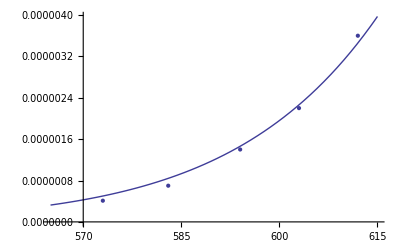

```mathematica
Show[plota,plotb]
```

```mathematica
Given equal amount of time, the amount of B formed relative to D is completely determined by the relative rate constants.
```

```mathematica
Since the reaction is a decomposition over a catalyst and the k- which leads the exponential term in the Arhenius relationship depends on the probabilities of intermolecular interactions, assume that the intermolecular interactions between the 2-propanol and oxide catalyst are equal in both reactions (kA0=bB0);
```

```mathematica
kB0=kA0;
```

```mathematica
Solve[Exp[-Ea/(R*T)]/Exp[-Eb/(R*T)]==.92,Eb]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Eb→0.693268 (25074.-1. T)}}

```mathematica
EbSolved[T_]=0.7841367133956885 (22168.328179308508-1. T);
```

```mathematica
EbSolved[573]
```

16933.7

```mathematica
Solve[Exp[-Ea/(R*T)]/Exp[-Eb/(R*T)]==.86,Eb]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Eb→1.254 (13862.-1. T)}}

```mathematica
EbSolved2[T_]=1.254001834409222 (13862.021189298639-1. T)
```

1.254 (13862.-1. T)

```mathematica
Solve[Exp[-Ea/(R*T)]/Exp[-Eb/(R*T)]==.81,Eb]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Eb→1.75202 (9921.7-1. T)}}

```mathematica
EbSolved3[T_]=1.752018942770861 (9921.696378755105-1. T)
```

1.75202 (9921.7-1. T)

```mathematica
EbSolved2[583]
```

16651.9

```mathematica
EbSolved3[594]
```

16342.3

```mathematica
EbSolved3[603]
```

16326.5

```mathematica
EbSolved3[612]
```

16310.8

```mathematica
Since the activation energy of the propene-forming reactionis expected to be temperature-independent, take the statistical average of these values in J/mol:
```

```mathematica
(EbSolved[573]+EbSolved2[583]+EbSolved3[594]+EbSolved3[603]+EbSolved3[612])/5
```

16513.

```mathematica
Problem #2:
```

```mathematica
For this CSTR, there is no accumulation since the rate of fluid flow into the reactor is equivalent to the rate of fluid flow out of the reactor.  So from minute to minute there is no material in the reactor from the previous minute.  If the solution can be crafted for a single minute, then it will be true for all minutes and therefore is a steady state solution.
```

```mathematica
kA=2.0 (* L/mol/min *);
```

```mathematica
kB=1.0 (* 1/min *);
```

```mathematica
A+B(->)^Subscript[k, 1] Desired Product
```

```mathematica
B(->)^Subscript[k, 2] Undesired Product
```

```mathematica
cAin=4 (* mol/L *);
```

```mathematica
cBin=2(* mol/L *);
```

```mathematica
fA=50 (* L/min *);
```

```mathematica
fB=50(* L/min *);
```

```mathematica
V=100 (* L *);
```

```mathematica
cA02=cAin*fA/V; (* mol/L *)
```

```mathematica
cB02=cBin*fB/V; (* mol/L *)
```

```mathematica
Then the two rate equations are written out:
```

```mathematica
Subscript[dc, A]/dt=-kA*cA*cB;
```

```mathematica
Subscript[dc, B]/dt=-kA*cA*cB-kB*cB;
```

```mathematica
cB can be written in terms of cA:
```

```mathematica
cB=cBin*fB/V-(cAin*fA/V-cA*fA/V)
```

-1+cA/2

```mathematica
DSolve[{cA2'[t]==-kA*cA2[t](cB02-(cA0-cA2[t])),cA2[0]==cA02},cA2[t],t]
```

{{cA2[t]→0.5/(0.25+1. t)}}

```mathematica
cA2[t_]=0.5/(0.25+1. t);
```

```mathematica
DSolve[{cB2'[t]==-kA*cB2[t](cB02-(cA0-cB2[t]))-kB*(cB02-(cA0-cB2[t])),cB2[0]==cB02},cB2[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{cB2[t]→0.333333/(-0.666667+1. 2.71828^t)}}

```mathematica
cB2[t_]=0.3333333333333333/(-0.6666666666666666+1. 2.718281828459045^t)
```

0.333333/(-0.666667+1. 2.71828^t)

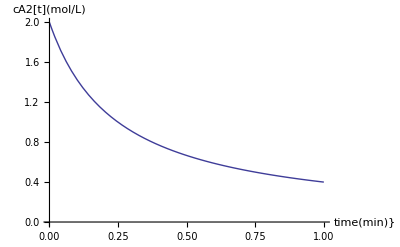

```mathematica
Plot[cA2[t],{t,0,1},PlotRange->{0,2},AxesLabel->{"time(min)}","cA2[t](mol/L)"}]
```

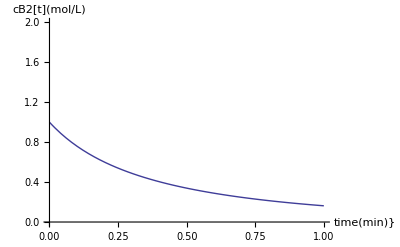

```mathematica
Plot[cB2[t],{t,0,1},PlotRange->{0,2},AxesLabel->{"time(min)}","cB2[t](mol/L)"}]
```

```mathematica
The steady state effluent concentrations in mol/L are therefore:
```

```mathematica
cA2[1]
```

0.4

```mathematica
cB2[1]
```

0.162474

```mathematica
Problem #3:
```

```mathematica
The rate expression is written:
```

```mathematica
Subscript[dc, A]/dt=-10^-2*cA^(1/2)
```

```mathematica
cA4in=0.0625 (* mol/L *);
```

```mathematica
cA40=cA4in/2 (*mol/L *)
```

0.03125

```mathematica
80% conversion will occur when the concentration is (mol/L):
```

```mathematica
cA4crit=(1-.8)cA40
```

0.00625

```mathematica
ϵ=(3-1)/Abs[-1]
```

2

```mathematica
τ[fa_]=cA40*∫_0^fa 1/(10^-2((cA40(1-f))/(1+f*ϵ))^(1/2))ⅆf
```

ConditionalExpression[17.6777 (1+(3 ArcSin[√(2/3)])/(√2)+(2 (-1+fa) √(1+2 fa)-3 √(2-2 fa) ArcSin[√(2/3) √(1-fa)])/(2 √((1-fa)/(1+2 fa)) √(1+2 fa))),(fa∉Reals&&(Re[1/fa]==0||Re[1/fa]≥1||2+Re[1/fa]≤0||1/fa∉Reals))||(Re[fa]<0&&1+2 Re[fa]>0&&(2+Re[1/fa]<0||1/fa∉Reals))||(Re[fa]<1&&Re[fa]>0&&(Re[1/fa]>1||1/fa∉Reals))]

```mathematica
τ  has units sec sinceit comes from the volume of the PFR/inlet flow rate=Volume/(Volume/time)=time and the units of the rate constant are sec.
```

```mathematica
τ[.8]
```

26.7373

```mathematica
Problem #4:
```

```mathematica
Let acethane be representaldehyde be represented by A, methane be represented by B, and carbon monoxide be represented by C.
```

```mathematica
The rate law for this system is given by:
```

```mathematica
Subscript[dc, A]/dt=-k6*cA^2
```

```mathematica
Let the reactor vessel have a volume of 1L.
```

```mathematica
V=1 (* L *);
```

```mathematica
T2=791(* K *);
```

```mathematica
P0=1(* atm *);
```

```mathematica
cA50=1 (* mol/L *);
```

```mathematica
ϵ2=(2-1)/Abs[-1]
```

1

```mathematica
The number of moles as a function of extent of reaction is:
```

```mathematica
n[x_]=1+x
```

1+x

```mathematica
Determining the extent of reaction associated with a pressure increase of 1.5:
```

```mathematica
Solve[n[x]==1.5,x]
```

{{x→0.5}}

```mathematica
Therefore specifying that the number of moles increases by a factor of 1.5 correlates to an extent of reaction of .5 at 197 sec.
```

```mathematica
Converting this time to minutes since the end production rate is given in minutes:
```

```mathematica
N[197/60,3] (* min *)
```

3.28

```mathematica
Clear[f]
```

```mathematica
DSolve[{f'[t]==-k5*((cA50(1+f[t]))/(1+f[t]*ϵ2))^2,f[0]==0},f[t],t]
```

{{f[t]→-k5 t}}

```mathematica
f[t_]=-k5 *t;
```

```mathematica
c5[t_]=cA50(1+f[t])
```

1-k5 t

```mathematica
Solve[c5[3.28]==.5,k5]
```

{{k5→0.152439}}

```mathematica
k5=0.1524390243902439;
```

```mathematica
For a conversion of 80%,c5[t] will be .2.  The time it takes for this to occur in minutesis:
```

```mathematica
Solve[c5[t]==.2,t]
```

{{t→5.248}}

```mathematica
A 1L reactor can create .8conversion of  acetaldehyde after 5.24 minutes.  In order to make 120L be converted at 80% in a single minute,you need to calculate the spacetime:
```

```mathematica
cA0*∫_0^(.8) 1/(k5*((cA50(1-f))/(1+f))^2)ⅆf
```

67.9763

```mathematica
Simply multiply by the inlet flowrate of 1L/min, which gives the neccesary volume from the definition of spacetime.
```

```mathematica
V=cA0*∫_0^(.8) 1/(k5*((cA50(1-f))/(1+f))^2)ⅆf
```

67.9763